```mathematica
SetAttributes[createPrimitive,HoldAll]
createPrimitive[patt_,expr_]:=Typeset`MakeBoxes[p:patt,fmt_,Graphics]:=With[{e=Cases[expr,Line[_],Infinity]},Typeset`MakeBoxes[Interpretation[e,p],fmt,Graphics]]
createPrimitive[Waved[a_,f_,pts_:Automatic]@Line[p:{{_,_?NumericQ}..}],Module[{fx,fy,distance=Prepend[Accumulate@Sqrt[Total@Transpose@((Rest@#-Most@#&@N@p)^2)],0.],normal},{fx,fy}=ListInterpolation[#,distance,InterpolationOrder->1]&/@Transpose@N@p;
normal=Sqrt[fx'[t]^2+fy'[t]^2];
ParametricPlot[{fx@t+a Sin[f t] fy'[t]/normal,fy@t-a Sin[f t] fx'[t]/normal},{t,0,distance[[-1]]},PlotPoints->pts]]]
```

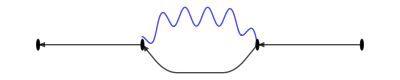

```mathematica
GraphPlot[{DirectedEdge[1,2,0],DirectedEdge[2,3,0],DirectedEdge[3,4,0],DirectedEdge[2,3,1]},EdgeShapeFunction->
(If[#2[[3]]==0,{Black,Arrowheads[{{0.03,0.6}}],Arrow[#]},{Blue,Waved[1/40,30]@Line[#1]}]&),VertexStyle->Black,VertexSize->0.03,Method->"SpringElectricalEmbedding"]
```

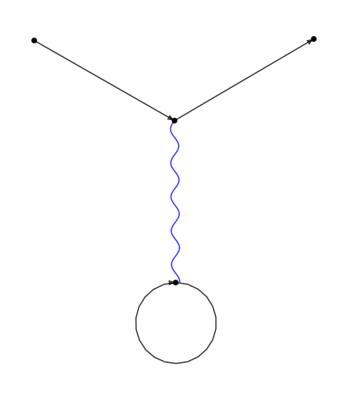

```mathematica
GraphPlot[{DirectedEdge[1,2,0],DirectedEdge[2,4,0],DirectedEdge[3,3,0],DirectedEdge[2,3,1]},EdgeShapeFunction->
(If[#2[[3]]==0,{Black,Arrowheads[{{0.03,0.6}}],Arrow[#]},{Blue,Waved[1/40,30]@Line[#1]}]&),VertexStyle->Black,VertexSize->0.03,Method->"SpringElectricalEmbedding"]
```

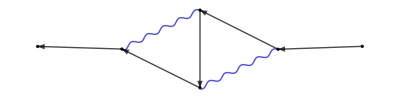

```mathematica
GraphPlot[{DirectedEdge[1,2,0],DirectedEdge[2,3,0],DirectedEdge[3,4,0],DirectedEdge[4,5,0],DirectedEdge[5,6,0],DirectedEdge[2,4,1],DirectedEdge[3,5,1]},EdgeShapeFunction->
(If[#2[[3]]==0,{Black,Arrowheads[{{0.03,0.6}}],Arrow[#]},{Blue,Waved[1/40,30]@Line[#1]}]&),VertexStyle->Black,VertexSize->0.03,Method->"SpringEmbedding"]
```

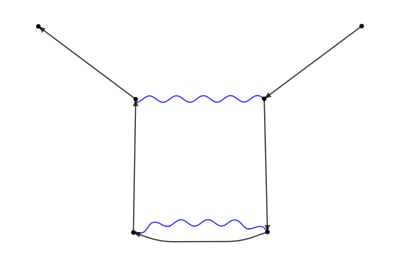

```mathematica
GraphPlot[{DirectedEdge[1,2,0],DirectedEdge[2,3,0],DirectedEdge[3,4,0],DirectedEdge[4,5,0],DirectedEdge[5,6,0],DirectedEdge[2,5,1],DirectedEdge[3,4,1]},EdgeShapeFunction->
(If[#2[[3]]==0,{Black,Arrowheads[{{0.03,0.6}}],Arrow[#]},{Blue,Waved[1/40,30]@Line[#1]}]&),VertexStyle->Black,VertexSize->0.03,Method->"SpringEmbedding"]
```

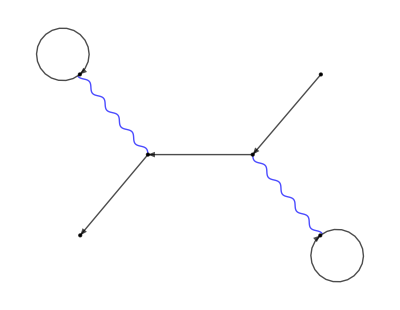

```mathematica
GraphPlot[{DirectedEdge[1,2,0],DirectedEdge[2,4,0],DirectedEdge[4,6,0],DirectedEdge[3,3,0],DirectedEdge[5,5,0],DirectedEdge[2,3,1],DirectedEdge[4,5,1]},EdgeShapeFunction->
(If[#2[[3]]==0,{Black,Arrowheads[{{0.03,0.6}}],Arrow[#]},{Blue,Waved[1/40,30]@Line[#1]}]&),VertexStyle->Black,VertexSize->0.03,Method->"SpringEmbedding"]
```

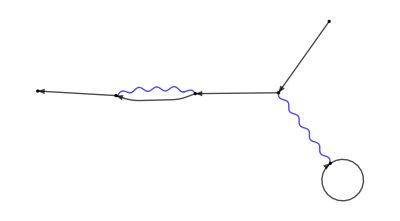

```mathematica
GraphPlot[{DirectedEdge[1,2,0],DirectedEdge[2,4,0],DirectedEdge[4,5,0],DirectedEdge[3,3,0],DirectedEdge[5,6,0],DirectedEdge[2,3,1],DirectedEdge[4,5,1]},EdgeShapeFunction->
(If[#2[[3]]==0,{Black,Arrowheads[{{0.03,0.6}}],Arrow[#]},{Blue,Waved[1/40,30]@Line[#1]}]&),VertexStyle->Black,VertexSize->0.03,Method->"SpringEmbedding"]
```

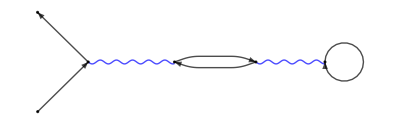

```mathematica
GraphPlot[{DirectedEdge[1,2,0],DirectedEdge[3,4,0],DirectedEdge[4,3,0],DirectedEdge[5,5,0],DirectedEdge[2,6,0],DirectedEdge[2,3,1],DirectedEdge[4,5,1]},EdgeShapeFunction->
(If[#2[[3]]==0,{Black,Arrowheads[{{0.03,0.6}}],Arrow[#]},{Blue,Waved[1/40,30]@Line[#1]}]&),VertexStyle->Black,VertexSize->0.03,Method->"SpringElectricalEmbedding"]
```

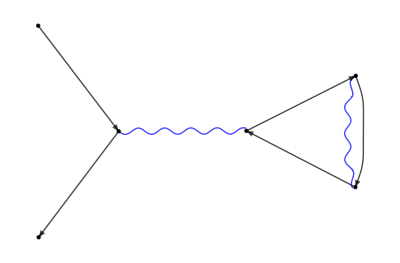

```mathematica
GraphPlot[{DirectedEdge[1,2,0],DirectedEdge[3,4,0],DirectedEdge[4,5,0],DirectedEdge[5,3,0],DirectedEdge[2,6,0],DirectedEdge[2,3,1],DirectedEdge[4,5,1]},EdgeShapeFunction->
(If[#2[[3]]==0,{Black,Arrowheads[{{0.03,0.6}}],Arrow[#]},{Blue,Waved[1/40,30]@Line[#1]}]&),VertexStyle->Black,VertexSize->0.03,Method->"SpringEmbedding"]
```

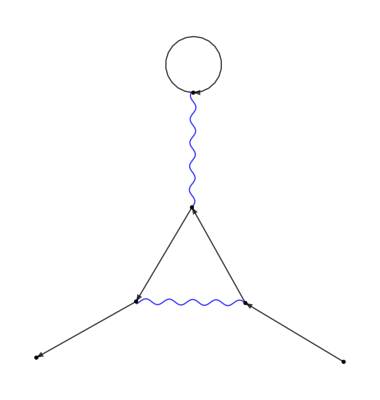

```mathematica
GraphPlot[{DirectedEdge[1,2,0],DirectedEdge[2,3,0],DirectedEdge[4,4,0],DirectedEdge[3,5,0],DirectedEdge[5,6,0],DirectedEdge[3,4,1],DirectedEdge[2,5,1]},EdgeShapeFunction->
(If[#2[[3]]==0,{Black,Arrowheads[{{0.03,0.6}}],Arrow[#]},{Blue,Waved[1/40,30]@Line[#1]}]&),VertexStyle->Black,VertexSize->0.03,Method->"SpringElectricalEmbedding"]
```

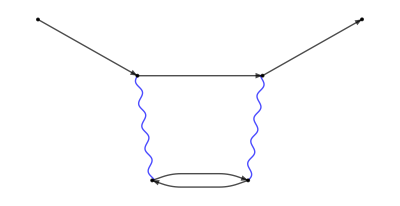

```mathematica
GraphPlot[{DirectedEdge[1,2,0],DirectedEdge[3,4,0],DirectedEdge[4,3,0],DirectedEdge[2,5,0],DirectedEdge[5,6,0],DirectedEdge[2,3,1],DirectedEdge[4,5,1]},EdgeShapeFunction->
(If[#2[[3]]==0,{Black,Arrowheads[{{0.03,0.6}}],Arrow[#]},{Blue,Waved[1/40,30]@Line[#1]}]&),VertexStyle->Black,VertexSize->0.03,Method->"SpringElectricalEmbedding"]
```